# Box integral

## B_3(s)

### Direct evaluation of the representations

Below we directly integrate the expression given in Ref[24] directly using MATHEMATICA.

```mathematica
valb3s1=6/((3+s)(2+s))Integrate[((1+Sec[t]^2)^(s/2+1)-1),{t,0,π/4}]
```

1/((2+s) (3+s))6 (-π/4+ⅈ AppellF1[1,1/2,-s/2,2,2,-2]-(2^((1+s)/2) AppellF1[1/2 (-1-s),-1/2,-s/2,(1-s)/2,1/2,-1/2])/(1+s)+2^(s/2) Hypergeometric2F1[1/2,-s/2,3/2,-1/2]-ⅈ Hypergeometric2F1[1,-s/2,3/2,-1]-(√π Gamma[-1/2-s/2] Hypergeometric2F1[-1/2-s/2,-s/2,1-s/2,-1])/(4 Gamma[1-s/2]))

### Conic Hulls

Below is the MB- representation of the B_3(s) integral

```mathematica
B3 =  (Gamma[1+2 z1] Gamma[1+s-2 z1-2 z2] Gamma[-s/2+z1+z2] Gamma[1+2 z2]Gamma[-z1]Gamma[-z2])/(Gamma[-s/2] Gamma[2+2 z1] Gamma[2+s-2 z1-2 z2]Gamma[2+2 z2]);
```

```mathematica
<<MBConicHulls.wl;
<<ROC2.wl;
```

Last Updated: 22^th December, 2022

Version 1.1 by S. Banik, S. Friot

Version 1.0 by B.Ananthanarayan, S.Banik, S.Friot, S.Ghosh

ROC2.wl v1.11
Authors : B. Ananthanarayan, Souvik Bera, S. Friot & Tanay Pathak

```mathematica
a3=  MBRep[1/Gamma[-s/2],{z1,z2},{α,β},{{-z1,-z2,1+2 z1,1+s-2 z1-2 z2,-s/2+z1+z2,1+2 z2},{2+2 z1,2+s-2 z1-2 z2,2+2 z2}}]
```

Non-Straight Contours.

{1/Gamma[-s/2],{z1,z2},{α,β},{{-z1,-z2,1+2 z1,1+s-2 z1-2 z2,-s/2+z1+z2,1+2 z2},{2+2 z1,2+s-2 z1-2 z2,2+2 z2}}}

```mathematica
b3 = ResolveMB[a3]
```

Degenerate case with 12 conic hulls

Found 6 series solutions.

Series Solution 1 :: Intersecting Conic Hulls {C_(1,2),C_(1,4),C_(4,6)}. The set of poles is :: {{n_1,n_2},{n_1,1/2+s/2-n_1+n_2/2},{1+s/2+n_1/2+n_2/2,-1/2-n_2/2}} with master series characteristic list and variables {{-n_1+n_2,n_1,n_1},{β,α/β}}.

Series Solution 2 :: Intersecting Conic Hulls {C_(1,2),C_(2,4),C_(3,4)}. The set of poles is :: {{n_1,n_2},{1/2+s/2-n_1+n_2/2,n_1},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2}} with master series characteristic list and variables {{n_1-n_2,n_2,n_2},{β/α,α}}.

Series Solution 3 :: Intersecting Conic Hulls {C_(1,5),C_(1,6),C_(4,6)}. The set of poles is :: {{n_1,s/2-n_1-n_2},{n_1,-1/2-n_2/2},{1+s/2+n_1/2+n_2/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1,-n_1+n_2,n_1},{1/β,α}}.

Series Solution 4 :: Intersecting Conic Hulls {C_(1,5),C_(3,6),C_(5,6)}. The set of poles is :: {{n_1,s/2-n_1-n_2},{-1/2-n_1/2,-1/2-n_2/2},{1/2+s/2-n_1+n_2/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_2,n_2,n_2},{1/α,α/β}}.

Series Solution 5 :: Intersecting Conic Hulls {C_(2,3),C_(2,5),C_(3,4)}. The set of poles is :: {{-1/2-n_2/2,n_1},{s/2-n_1-n_2,n_1},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2}} with master series characteristic list and variables {{n_1,-n_1+n_2,n_1},{1/α,β}}.

Series Solution 6 :: Intersecting Conic Hulls {C_(2,5),C_(3,5),C_(3,6)}. The set of poles is :: {{s/2-n_1-n_2,n_1},{-1/2-n_1/2,1/2+s/2+n_1/2-n_2},{-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_2,n_1-n_2,n_2},{1/β,β/α}}.

Time Taken 0.485404 seconds

{{{1,2,11},{1,6,8},{3,4,11},{3,10,12},{5,7,8},{7,9,10}},{{1,2},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{3,4},{3,5},{3,6},{4,6},{5,6}},{{n_1,n_2},{n_1,1/2+s/2-n_1+n_2/2},{n_1,s/2-n_1-n_2},{n_1,-1/2-n_2/2},{-1/2-n_2/2,n_1},{1/2+s/2-n_1+n_2/2,n_1},{s/2-n_1-n_2,n_1},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2},{-1/2-n_1/2,1/2+s/2+n_1/2-n_2},{-1/2-n_1/2,-1/2-n_2/2},{1+s/2+n_1/2+n_2/2,-1/2-n_2/2},{1/2+s/2-n_1+n_2/2,-1/2-n_2/2}},Degenerate case with 12 conic hulls,{Series Solution 1 :: Intersecting Conic Hulls {C_(1,2),C_(1,4),C_(4,6)}. The set of poles is :: {{n_1,n_2},{n_1,1/2+s/2-n_1+n_2/2},{1+s/2+n_1/2+n_2/2,-1/2-n_2/2}} with master series characteristic list and variables {{-n_1+n_2,n_1,n_1},{β,α/β}}.,Series Solution 2 :: Intersecting Conic Hulls {C_(1,2),C_(2,4),C_(3,4)}. The set of poles is :: {{n_1,n_2},{1/2+s/2-n_1+n_2/2,n_1},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2}} with master series characteristic list and variables {{n_1-n_2,n_2,n_2},{β/α,α}}.,Series Solution 3 :: Intersecting Conic Hulls {C_(1,5),C_(1,6),C_(4,6)}. The set of poles is :: {{n_1,s/2-n_1-n_2},{n_1,-1/2-n_2/2},{1+s/2+n_1/2+n_2/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1,-n_1+n_2,n_1},{1/β,α}}.,Series Solution 4 :: Intersecting Conic Hulls {C_(1,5),C_(3,6),C_(5,6)}. The set of poles is :: {{n_1,s/2-n_1-n_2},{-1/2-n_1/2,-1/2-n_2/2},{1/2+s/2-n_1+n_2/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_2,n_2,n_2},{1/α,α/β}}.,Series Solution 5 :: Intersecting Conic Hulls {C_(2,3),C_(2,5),C_(3,4)}. The set of poles is :: {{-1/2-n_2/2,n_1},{s/2-n_1-n_2,n_1},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2}} with master series characteristic list and variables {{n_1,-n_1+n_2,n_1},{1/α,β}}.,Series Solution 6 :: Intersecting Conic Hulls {C_(2,5),C_(3,5),C_(3,6)}. The set of poles is :: {{s/2-n_1-n_2,n_1},{-1/2-n_1/2,1/2+s/2+n_1/2-n_2},{-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_2,n_1-n_2,n_2},{1/β,β/α}}.},{1,1,-1,-1,1,-1,1,-1,1,1,-1,1,0,0,0},6,{1/Gamma[-s/2],{z1,z2},{α,β},{{-z1,-z2,1+2 z1,1+s-2 z1-2 z2,-s/2+z1+z2,1+2 z2},{2+2 z1,2+s-2 z1-2 z2,2+2 z2}}}}

#### First solution

For our purpose we will take the first series solution obtained using the CHMB method.

```mathematica
Evaluateb31=EvaluateSeries[b3,{},1];
```

The series solution is a sum of the following 3 series.

Series Number 1 :: ((-1)^(n_1+n_2) α^n_1 β^n_2 Gamma[1+2 n_1] Gamma[1+s-2 n_1-2 n_2] Gamma[-s/2+n_1+n_2] Gamma[1+2 n_2])/(Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[2+s-2 n_1-2 n_2] Gamma[1+n_2] Gamma[2 (1+n_2)]) valid for n_1≥0&&n_2≥0

Series Number 2 :: ((-1)^(n_1+n_2) α^n_1 β^(1/2 (1+s-2 n_1+n_2)) Gamma[1+2 n_1] Gamma[-1/2-s/2+n_1-n_2/2] Gamma[1/2 (1+n_2)] Gamma[2+s-2 n_1+n_2])/(2 Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[1-n_2] Gamma[1+n_2] Gamma[3+s-2 n_1+n_2]) valid for n_2<1

Series Number 3 :: ((-1)^(n_1+n_2) α^(1/2 (2+s+n_1+n_2)) β^(1/2 (-1-n_2)) Gamma[1/2 (1+n_1)] Gamma[1/2 (-2-s-n_1-n_2)] Gamma[1/2 (1+n_2)] Gamma[3+s+n_1+n_2])/(4 Gamma[-s/2] Gamma[1-n_1] Gamma[1+n_1] Gamma[1-n_2] Gamma[1+n_2] Gamma[4+s+n_1+n_2]) valid for n_1<1&&n_2<1

Time Taken 0.391472 seconds

Series number : 1

```mathematica
ser1= ((-1)^(Subscript[n, 1]+Subscript[n, 2]) α^Subscript[n, 1] β^Subscript[n, 2] Gamma[1+2 Subscript[n, 1]] Gamma[1+s-2 Subscript[n, 1]-2 Subscript[n, 2]] Gamma[-s/2+Subscript[n, 1]+Subscript[n, 2]] Gamma[1+2 Subscript[n, 2]])/(Gamma[-s/2] Gamma[1+Subscript[n, 1]] Gamma[2 (1+Subscript[n, 1])] Gamma[2+s-2 Subscript[n, 1]-2 Subscript[n, 2]] Gamma[1+Subscript[n, 2]] Gamma[2 (1+Subscript[n, 2])])//FullSimplify
```

((-1)^(n_1+n_2) α^n_1 β^n_2 Gamma[-s/2+n_1+n_2])/(Gamma[-s/2] Gamma[1+n_1] Gamma[1+n_2] (1+2 n_1) (1+s-2 n_1-2 n_2) (1+2 n_2))

Below we calculate its region of convergence using the ROC2.wl package.

```mathematica
ROC2[m,n,{m+n,m+n,m,n},{m+n,m,n},α,β]
```

{{R,S}, Cartesian Curve, ROC -> ,{1,1},{Abs[α]+Abs[β]==1},{Abs[α]<1&&Abs[β]<1&&Abs[β]<1-Abs[α]}}

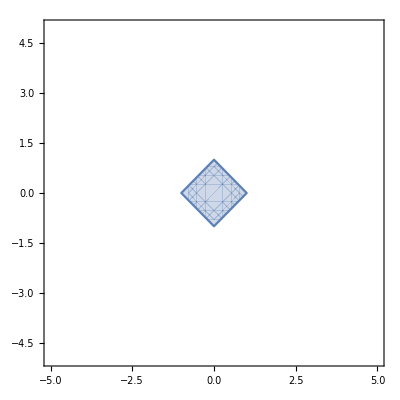

```mathematica
RegionPlot[Abs[α]<1&&Abs[β]<1&&Abs[β]<1-Abs[α],{α,-5,5},{β,-5,5}]
```

In the above plot of region of convergence we see that our point of interest (1,1) lies outside the region of convergence of the series and hence we need to find its suitable analytic continuation.

Series number : 2, it is valid for only n_2 = 0

```mathematica
ser2=Sum[((-1)^(Subscript[n, 1]+Subscript[n, 2]) α^Subscript[n, 1] β^(1/2 (1+s-2 Subscript[n, 1]+Subscript[n, 2])) Gamma[1+2 Subscript[n, 1]] Gamma[-1/2-s/2+Subscript[n, 1]-Subscript[n, 2]/2] Gamma[1/2 (1+Subscript[n, 2])] Gamma[2+s-2 Subscript[n, 1]+Subscript[n, 2]])/(2 Gamma[-s/2] Gamma[1+Subscript[n, 1]] Gamma[2 (1+Subscript[n, 1])] Gamma[1-Subscript[n, 2]] Gamma[1+Subscript[n, 2]] Gamma[3+s-2 Subscript[n, 1]+Subscript[n, 2]])/.Subscript[n, 2]-> 0,{Subscript[n, 1],0,Infinity}]/.α-> 1/.β-> 1//Simplify
```

(√π Gamma[1/2 (-1-s)] Gamma[2+s] ((2+s) Hypergeometric2F1[1/2,-1/2-s/2,3/2,-1]+Hypergeometric2F1[-1-s/2,-1/2-s/2,-s/2,-1]))/(2 (3+s) Gamma[-s/2] Gamma[3+s])

Series number : 3,  is valid for only n_1,n_2 = 0

```mathematica
ser3=((-1)^(Subscript[n, 1]+Subscript[n, 2]) α^(1/2 (2+s+Subscript[n, 1]+Subscript[n, 2])) β^(1/2 (-1-Subscript[n, 2])) Gamma[1/2 (1+Subscript[n, 1])] Gamma[1/2 (-2-s-Subscript[n, 1]-Subscript[n, 2])] Gamma[1/2 (1+Subscript[n, 2])] Gamma[3+s+Subscript[n, 1]+Subscript[n, 2]])/(4 Gamma[-s/2] Gamma[1-Subscript[n, 1]] Gamma[1+Subscript[n, 1]] Gamma[1-Subscript[n, 2]] Gamma[1+Subscript[n, 2]] Gamma[4+s+Subscript[n, 1]+Subscript[n, 2]])/.Subscript[n, 1]-> 0/.Subscript[n, 2]-> 0/.α-> 1/.β-> 1//FullSimplify
```

-π/(2 (6+5 s+s^2))

#### Other series solutions

One can also use other series solutions as the starting point.

Below we give all the other series solutions that are obtained using the MBConicHulls.wl package.

```mathematica
Evaluateb32=EvaluateSeries[b3,{},2];
```

The series solution is a sum of the following 3 series.

Series Number 1 :: ((-1)^(n_1+n_2) α^n_1 β^n_2 Gamma[1+2 n_1] Gamma[1+s-2 n_1-2 n_2] Gamma[-s/2+n_1+n_2] Gamma[1+2 n_2])/(Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[2+s-2 n_1-2 n_2] Gamma[1+n_2] Gamma[2 (1+n_2)]) valid for n_1≥0&&n_2≥0

Series Number 2 :: ((-1)^(n_1+n_2) α^(1/2 (1+s-2 n_1+n_2)) β^n_1 Gamma[1+2 n_1] Gamma[-1/2-s/2+n_1-n_2/2] Gamma[1/2 (1+n_2)] Gamma[2+s-2 n_1+n_2])/(2 Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[1-n_2] Gamma[1+n_2] Gamma[3+s-2 n_1+n_2]) valid for n_2<1

Series Number 3 :: ((-1)^(n_1+n_2) α^(1/2 (-1-n_1)) β^(1/2 (2+s+n_1+n_2)) Gamma[1/2 (1+n_1)] Gamma[1/2 (-2-s-n_1-n_2)] Gamma[1/2 (1+n_2)] Gamma[3+s+n_1+n_2])/(4 Gamma[-s/2] Gamma[1-n_1] Gamma[1+n_1] Gamma[1-n_2] Gamma[1+n_2] Gamma[4+s+n_1+n_2]) valid for n_1<1&&n_2<1

Time Taken 0.343049 seconds

```mathematica
Evaluateb33=EvaluateSeries[b3,{},3];
```

The series solution is a sum of the following 3 series.

Series Number 1 :: ((-1)^(n_1+n_2) α^n_1 β^(1/2 (s-2 n_1-2 n_2)) Gamma[1+2 n_1] Gamma[1+s-2 n_1-2 n_2] Gamma[-s/2+n_1+n_2] Gamma[1+2 n_2])/(Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[2+s-2 n_1-2 n_2] Gamma[1+n_2] Gamma[2 (1+n_2)]) valid for n_1≥0&&n_2≥0

Series Number 2 :: ((-1)^(n_1+n_2) α^n_1 β^(1/2 (-1-n_2)) Gamma[1+2 n_1] Gamma[-1/2-s/2+n_1-n_2/2] Gamma[1/2 (1+n_2)] Gamma[2+s-2 n_1+n_2])/(2 Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[1-n_2] Gamma[1+n_2] Gamma[3+s-2 n_1+n_2]) valid for n_2<1

Series Number 3 :: ((-1)^(n_1+n_2) α^(1/2 (2+s+n_1+n_2)) β^(1/2 (-1-n_2)) Gamma[1/2 (1+n_1)] Gamma[1/2 (-2-s-n_1-n_2)] Gamma[1/2 (1+n_2)] Gamma[3+s+n_1+n_2])/(4 Gamma[-s/2] Gamma[1-n_1] Gamma[1+n_1] Gamma[1-n_2] Gamma[1+n_2] Gamma[4+s+n_1+n_2]) valid for n_1<1&&n_2<1

Time Taken 0.293571 seconds

```mathematica
Evaluateb34=EvaluateSeries[b3,{},4];
```

The series solution is a sum of the following 3 series.

Series Number 1 :: ((-1)^(n_1+n_2) α^n_1 β^(1/2 (s-2 n_1-2 n_2)) Gamma[1+2 n_1] Gamma[1+s-2 n_1-2 n_2] Gamma[-s/2+n_1+n_2] Gamma[1+2 n_2])/(Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[2+s-2 n_1-2 n_2] Gamma[1+n_2] Gamma[2 (1+n_2)]) valid for n_1≥0&&n_2≥0

Series Number 2 :: ((-1)^(n_1+n_2) α^(1/2 (-1-n_1)) β^(1/2 (-1-n_2)) Gamma[1/2 (1+n_1)] Gamma[1/2 (-2-s-n_1-n_2)] Gamma[1/2 (1+n_2)] Gamma[3+s+n_1+n_2])/(4 Gamma[-s/2] Gamma[1-n_1] Gamma[1+n_1] Gamma[1-n_2] Gamma[1+n_2] Gamma[4+s+n_1+n_2]) valid for n_1<1&&n_2<1

Series Number 3 :: ((-1)^(n_1+n_2) α^(1/2 (1+s-2 n_1+n_2)) β^(1/2 (-1-n_2)) Gamma[1+2 n_1] Gamma[-1/2-s/2+n_1-n_2/2] Gamma[1/2 (1+n_2)] Gamma[2+s-2 n_1+n_2])/(2 Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[1-n_2] Gamma[1+n_2] Gamma[3+s-2 n_1+n_2]) valid for n_2<1

Time Taken 0.292844 seconds

```mathematica
Evaluateb35=EvaluateSeries[b3,{},5];
```

The series solution is a sum of the following 3 series.

Series Number 1 :: ((-1)^(n_1+n_2) α^(-1/2-n_2/2) β^n_1 Gamma[1+2 n_1] Gamma[-1/2-s/2+n_1-n_2/2] Gamma[1/2 (1+n_2)] Gamma[2+s-2 n_1+n_2])/(2 Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[1-n_2] Gamma[1+n_2] Gamma[3+s-2 n_1+n_2]) valid for n_2<1

Series Number 2 :: ((-1)^(n_1+n_2) α^(1/2 (s-2 n_1-2 n_2)) β^n_1 Gamma[1+2 n_1] Gamma[1+s-2 n_1-2 n_2] Gamma[-s/2+n_1+n_2] Gamma[1+2 n_2])/(Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[2+s-2 n_1-2 n_2] Gamma[1+n_2] Gamma[2 (1+n_2)]) valid for n_1≥0&&n_2≥0

Series Number 3 :: ((-1)^(n_1+n_2) α^(1/2 (-1-n_1)) β^(1/2 (2+s+n_1+n_2)) Gamma[1/2 (1+n_1)] Gamma[1/2 (-2-s-n_1-n_2)] Gamma[1/2 (1+n_2)] Gamma[3+s+n_1+n_2])/(4 Gamma[-s/2] Gamma[1-n_1] Gamma[1+n_1] Gamma[1-n_2] Gamma[1+n_2] Gamma[4+s+n_1+n_2]) valid for n_1<1&&n_2<1

Time Taken 0.279157 seconds

```mathematica
Evaluateb36=EvaluateSeries[b3,{},6];
```

The series solution is a sum of the following 3 series.

Series Number 1 :: ((-1)^(n_1+n_2) α^(1/2 (s-2 n_1-2 n_2)) β^n_1 Gamma[1+2 n_1] Gamma[1+s-2 n_1-2 n_2] Gamma[-s/2+n_1+n_2] Gamma[1+2 n_2])/(Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[2+s-2 n_1-2 n_2] Gamma[1+n_2] Gamma[2+2 n_2]) valid for n_1≥0&&n_2≥0

Series Number 2 :: ((-1)^(n_1+n_2) α^(1/2 (-1-n_1)) β^(1/2 (1+s+n_1-2 n_2)) Gamma[1/2 (1+n_1)] Gamma[2+s+n_1-2 n_2] Gamma[-1/2-s/2-n_1/2+n_2] Gamma[1+2 n_2])/(2 Gamma[-s/2] Gamma[1-n_1] Gamma[1+n_1] Gamma[3+s+n_1-2 n_2] Gamma[1+n_2] Gamma[2+2 n_2]) valid for n_1<1

Series Number 3 :: ((-1)^(n_1+n_2) α^(1/2 (-1-n_1)) β^(-1/2-n_2/2) Gamma[1/2 (1+n_1)] Gamma[1/2 (-2-s-n_1-n_2)] Gamma[1/2 (1+n_2)] Gamma[3+s+n_1+n_2])/(4 Gamma[-s/2] Gamma[1-n_1] Gamma[1+n_1] Gamma[1-n_2] Gamma[1+n_2] Gamma[4+s+n_1+n_2]) valid for n_1<1&&n_2<1

Time Taken 0.400466 seconds

#### Analytic continuation

We note that the only the first series “ser1” is required to be analytically continued. All the other series converges for our point of interest i.e. α = 1, β = 1

```mathematica
ser1= ((-1)^(Subscript[n, 1]+Subscript[n, 2]) α^Subscript[n, 1] β^Subscript[n, 2] Gamma[1+2 Subscript[n, 1]] Gamma[1+s-2 Subscript[n, 1]-2 Subscript[n, 2]] Gamma[-s/2+Subscript[n, 1]+Subscript[n, 2]] Gamma[1+2 Subscript[n, 2]])/(Gamma[-s/2] Subscript[n, 1]!Subscript[n, 2]! Gamma[2 (1+Subscript[n, 1])] Gamma[2+s-2 Subscript[n, 1]-2 Subscript[n, 2]]  Gamma[2 (1+Subscript[n, 2])])
```

((-1)^(n_1+n_2) α^n_1 β^n_2 Gamma[1+2 n_1] Gamma[1+s-2 n_1-2 n_2] Gamma[-s/2+n_1+n_2] Gamma[1+2 n_2])/(n_1! n_2! Gamma[-s/2] Gamma[2 (1+n_1)] Gamma[2+s-2 n_1-2 n_2] Gamma[2 (1+n_2)])

```mathematica
<<Olsson.wl
```

Olsson.wl v1.21
Authors : B. Ananthanarayan, Souvik Bera, S. Friot & Tanay Pathak

ROC2.wl v1.11
Authors : B. Ananthanarayan, Souvik Bera, S. Friot & Tanay Pathak

```mathematica
ser1p=Simplify/@((ser1//.gammatoPoch[{Subscript[n, 1],Subscript[n, 2]}]))//.positivepoch[{Subscript[n, 1]+Subscript[n, 2]}]//.Pochdim//Simplify
```

((-1)^(n_1+n_2) α^n_1 β^n_2 Gamma[1+s] Pochhammer[1/2,n_1] Pochhammer[1/2,n_2] Pochhammer[1/2 (-1-s),n_1+n_2] Pochhammer[-s/2,n_1+n_2])/(n_1! n_2! Gamma[2+s] Pochhammer[3/2,n_1] Pochhammer[3/2,n_2] Pochhammer[1/2-s/2,n_1+n_2])

We can recognize it as a KdF function

```mathematica
serrecog2var[{Subscript[n, 1],Subscript[n, 2]},ser1p]
```

(Gamma[1+s] KdF[{{{1/2 (-1-s),-s/2},{1/2},{1/2}},{{1/2-s/2},{3/2},{3/2}}},{-α,-β}])/Gamma[2+s]

We then use Olsson.wl package to sum over the index n_1

```mathematica
serhyp1=Olsson[1,{Subscript[n, 1],Subscript[n, 1]},ser1p, sum-> True]
```

((-1)^n_2 β^n_2 Gamma[1+s] Pochhammer[1/2,n_2] Pochhammer[1/2 (-1-s),n_2] Pochhammer[-s/2,n_2] (HypergeometricPFQ[{-1/2-s/2+n_2,-s/2+n_2},{1/2-s/2+n_2},-α]/(2+s-2 n_2)+(HypergeometricPFQ[{1/2,-s/2+n_2},{3/2},-α] (1+s-2 n_2))/(2+s-2 n_2)))/(n_2! Gamma[2+s] Pochhammer[3/2,n_2] Pochhammer[(1-s)/2,n_2])

We write the above result as a list to facilitate our calculations

```mathematica
serlist= {((-1)^Subscript[n, 2] β^Subscript[n, 2] Pochhammer[1/2,Subscript[n, 2]] Pochhammer[1/2 (-1-s),Subscript[n, 2]] Pochhammer[-s/2,Subscript[n, 2]] ((HypergeometricPFQ[{1/2,-s/2+Subscript[n, 2]},{3/2},-α] (1+s-2 Subscript[n, 2]))/(2+s-2 Subscript[n, 2])))/(Subscript[n, 2]! (1+s) Pochhammer[3/2,Subscript[n, 2]] Pochhammer[(1-s)/2,Subscript[n, 2]]),((-1)^Subscript[n, 2] β^Subscript[n, 2]  Pochhammer[1/2,Subscript[n, 2]] Pochhammer[1/2 (-1-s),Subscript[n, 2]] Pochhammer[-s/2,Subscript[n, 2]] (HypergeometricPFQ[{-1/2-s/2+Subscript[n, 2],-s/2+Subscript[n, 2]},{1/2-s/2+Subscript[n, 2]},-α]/(2+s-2 Subscript[n, 2])))/(Subscript[n, 2]! (1+s) Pochhammer[3/2,Subscript[n, 2]] Pochhammer[(1-s)/2,Subscript[n, 2]])};
```

We now take the first series in the above list

```mathematica
serac1=Olsson[1,{Subscript[n, 1],Subscript[n, 2]},serlist[[1]], PET1-> True,sim-> True]//Simplify
```

((α/(1+α))^n_1 β^n_2 Pochhammer[1/2,n_1] Pochhammer[1/2,n_2] Pochhammer[1/2 (-1-s),n_2]^2 Pochhammer[-s/2,n_2] Pochhammer[(3+s)/2,n_1-n_2] (1+s-2 n_2))/((1+s) √(1+α) n_1! n_2! Pochhammer[3/2,n_1] Pochhammer[3/2,n_2] Pochhammer[(1-s)/2,n_2] (2+s-2 n_2))

Second series in the above list

```mathematica
serac2=Olsson[1,{Subscript[n, 1],Subscript[n, 2]},serlist[[2]], PET1-> True,sim-> True]//Simplify
```

((-1)^n_2 (α/(1+α))^n_1 (1+α)^(1/2 (1+s-2 n_2)) β^n_2 Pochhammer[1/2,n_1] Pochhammer[1/2,n_2] Pochhammer[1/2 (-1-s),n_1+n_2] Pochhammer[-s/2,n_2])/((1+s) n_1! n_2! Pochhammer[3/2,n_2] Pochhammer[(1-s)/2,n_1+n_2] (2+s-2 n_2))

Final result for B_3(s) integral is given as follows:

```mathematica
B3s=( serac1+serac2)+ser2+ser3;
```

As a quick Numerical check consider the value of B_3(1). It is given in literature as (-√3)/6-π/12= -0.550475...

Using the result we have get

```mathematica
N[Sum[((serac1+serac2)/.{α-> 1,β-> 1,s->-5}),{Subscript[n, 1],0,200},{Subscript[n, 2],0,200}]+Limit[ser2,s-> -5]+(ser3/.s-> -5)]
```

-0.550888

## B_4(s)

```mathematica
B4 =  (Gamma[1+2 z1]Gamma[1+2 z2]Gamma[1+2 z3] Gamma[1+s-2 z1-2 z2-2z3] Gamma[-s/2+z1+z2+z3] Gamma[-z1]Gamma[-z2]Gamma[-z3])/(Gamma[-s/2] Gamma[2+2 z1] Gamma[2+2 z2]Gamma[2+2 z3]Gamma[2+s-2 z1-2 z2-2z3]);
```

```mathematica
<<MBConicHulls.wl
```

Last Updated: 22^th December, 2022

Version 1.1 by S. Banik, S. Friot

Version 1.0 by B.Ananthanarayan, S.Banik, S.Friot, S.Ghosh

```mathematica
a4=  MBRep[1/Gamma[-s/2],{z1,z2,z3},{α,β,γ},{{-z1,-z2,-z3,1+2 z1,1+2 z2,1+2z3,1+s-2 z1-2 z2-2z3,-s/2+z1+z2+z3},{2+2 z1,2+2 z2,2+2z3,2+s-2 z1-2 z2-2z3}}]
```

Non-Straight Contours.

{1/Gamma[-s/2],{z1,z2,z3},{α,β,γ},{{-z1,-z2,-z3,1+2 z1,1+2 z2,1+2 z3,1+s-2 z1-2 z2-2 z3,-s/2+z1+z2+z3},{2+2 z1,2+2 z2,2+2 z3,2+s-2 z1-2 z2-2 z3}}}

```mathematica
b4 = ResolveMB[a4]
```

Degenerate case with 32 conic hulls

Found 24 series solutions.

Series Solution 1 :: Intersecting Conic Hulls {C_(1,2,3),C_(1,2,7),C_(1,6,7),C_(5,6,7)}. The set of poles is :: {{n_1,n_2,n_3},{n_1,n_2,1/2+s/2-n_1-n_2+n_3/2},{n_1,1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{-n_2+n_3,-n_1+n_2,n_1,n_1,n_2},{γ,β/γ,α/β}}.

Series Solution 2 :: Intersecting Conic Hulls {C_(1,2,3),C_(1,2,7),C_(2,6,7),C_(4,6,7)}. The set of poles is :: {{n_1,n_2,n_3},{n_1,n_2,1/2+s/2-n_1-n_2+n_3/2},{1+s/2-n_1+n_2/2+n_3/2,n_1,-1/2-n_2/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_2-n_3,-n_1+n_3,n_1,n_1,n_3},{γ,β/α,α/γ}}.

Series Solution 3 :: Intersecting Conic Hulls {C_(1,2,3),C_(1,3,7),C_(1,5,7),C_(5,6,7)}. The set of poles is :: {{n_1,n_2,n_3},{n_1,1/2+s/2-n_1-n_2+n_3/2,n_2},{n_1,-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_2,-n_1+n_3,n_2,n_1,n_2},{γ/β,β,α/γ}}.

Series Solution 4 :: Intersecting Conic Hulls {C_(1,2,3),C_(1,3,7),C_(3,5,7),C_(4,5,7)}. The set of poles is :: {{n_1,n_2,n_3},{n_1,1/2+s/2-n_1-n_2+n_3/2,n_2},{1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_1-n_3,-n_2+n_3,n_2,n_2,n_3},{γ/α,β,α/β}}.

Series Solution 5 :: Intersecting Conic Hulls {C_(1,2,3),C_(2,3,7),C_(2,4,7),C_(4,6,7)}. The set of poles is :: {{n_1,n_2,n_3},{1/2+s/2-n_1-n_2+n_3/2,n_1,n_2},{-1/2-n_2/2,n_1,1+s/2-n_1+n_2/2+n_3/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,-n_1+n_2,n_3,n_1,n_3},{γ/α,β/γ,α}}.

Series Solution 6 :: Intersecting Conic Hulls {C_(1,2,3),C_(2,3,7),C_(3,4,7),C_(4,5,7)}. The set of poles is :: {{n_1,n_2,n_3},{1/2+s/2-n_1-n_2+n_3/2,n_1,n_2},{-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_2-n_3,n_1-n_2,n_3,n_2,n_3},{γ/β,β/α,α}}.

Series Solution 7 :: Intersecting Conic Hulls {C_(1,2,6),C_(1,2,8),C_(1,6,7),C_(5,6,7)}. The set of poles is :: {{n_1,n_2,-1/2-n_3/2},{n_1,n_2,s/2-n_1-n_2-n_3},{n_1,1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,n_2,-n_2+n_3,n_2,n_3},{α/β,1/γ,β}}.

Series Solution 8 :: Intersecting Conic Hulls {C_(1,2,6),C_(1,2,8),C_(2,6,7),C_(4,6,7)}. The set of poles is :: {{n_1,n_2,-1/2-n_3/2},{n_1,n_2,s/2-n_1-n_2-n_3},{1+s/2-n_1+n_2/2+n_3/2,n_1,-1/2-n_2/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,n_2,-n_2+n_3,n_2,n_3},{β/α,1/γ,α}}.

Series Solution 9 :: Intersecting Conic Hulls {C_(1,2,8),C_(1,5,6),C_(1,6,8),C_(5,6,7)}. The set of poles is :: {{n_1,n_2,s/2-n_1-n_2-n_3},{n_1,-1/2-n_2/2,-1/2-n_3/2},{n_1,1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{-n_1+n_2,n_1,-n_2+n_3,n_1,n_2},{β/γ,1/β,α}}.

Series Solution 10 :: Intersecting Conic Hulls {C_(1,2,8),C_(1,6,8),C_(4,5,6),C_(5,6,8)}. The set of poles is :: {{n_1,n_2,s/2-n_1-n_2-n_3},{n_1,1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{1+s/2+n_1/2+n_2/2-n_3,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,-n_2+n_3,n_2,n_2,n_3},{1/α,β/γ,α/β}}.

Series Solution 11 :: Intersecting Conic Hulls {C_(1,2,8),C_(2,4,6),C_(2,6,8),C_(4,6,7)}. The set of poles is :: {{n_1,n_2,s/2-n_1-n_2-n_3},{-1/2-n_2/2,n_1,-1/2-n_3/2},{1/2+s/2-n_1+n_2/2-n_3,n_1,-1/2-n_2/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{-n_1+n_3,n_1,n_2-n_3,n_1,n_3},{α/γ,β,1/α}}.

Series Solution 12 :: Intersecting Conic Hulls {C_(1,2,8),C_(2,6,8),C_(4,5,6),C_(4,6,8)}. The set of poles is :: {{n_1,n_2,s/2-n_1-n_2-n_3},{1/2+s/2-n_1+n_2/2-n_3,n_1,-1/2-n_2/2},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2-n_3,-1/2-n_2/2}} with master series characteristic list and variables {{n_2-n_3,n_1-n_2,n_3,n_2,n_3},{1/β,β/α,α/γ}}.

Series Solution 13 :: Intersecting Conic Hulls {C_(1,3,5),C_(1,3,8),C_(1,5,7),C_(5,6,7)}. The set of poles is :: {{n_1,-1/2-n_3/2,n_2},{n_1,s/2-n_1-n_2-n_3,n_2},{n_1,-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_3,n_1-n_2,n_2-n_3,n_2,n_3},{α/γ,γ,1/β}}.

Series Solution 14 :: Intersecting Conic Hulls {C_(1,3,5),C_(1,3,8),C_(3,5,7),C_(4,5,7)}. The set of poles is :: {{n_1,-1/2-n_3/2,n_2},{n_1,s/2-n_1-n_2-n_3,n_2},{1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_1-n_3,n_2,-n_2+n_3,n_2,n_3},{γ/α,1/β,α}}.

Series Solution 15 :: Intersecting Conic Hulls {C_(1,3,8),C_(1,5,6),C_(1,5,8),C_(5,6,7)}. The set of poles is :: {{n_1,s/2-n_1-n_2-n_3,n_2},{n_1,-1/2-n_2/2,-1/2-n_3/2},{n_1,-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1,-n_1+n_2,-n_2+n_3,n_1,n_2},{γ/β,1/γ,α}}.

Series Solution 16 :: Intersecting Conic Hulls {C_(1,3,8),C_(1,5,8),C_(4,5,6),C_(5,6,8)}. The set of poles is :: {{n_1,s/2-n_1-n_2-n_3,n_2},{n_1,-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{1+s/2+n_1/2+n_2/2-n_3,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,n_2,-n_2+n_3,n_2,n_3},{1/α,γ/β,α/γ}}.

Series Solution 17 :: Intersecting Conic Hulls {C_(1,3,8),C_(3,4,5),C_(3,5,8),C_(4,5,7)}. The set of poles is :: {{n_1,s/2-n_1-n_2-n_3,n_2},{-1/2-n_2/2,-1/2-n_3/2,n_1},{1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{-n_1+n_3,n_1,n_2-n_3,n_1,n_3},{α/β,γ,1/α}}.

Series Solution 18 :: Intersecting Conic Hulls {C_(1,3,8),C_(3,5,8),C_(4,5,6),C_(4,5,8)}. The set of poles is :: {{n_1,s/2-n_1-n_2-n_3,n_2},{1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,-1/2-n_2/2,1+s/2+n_1/2+n_2/2-n_3}} with master series characteristic list and variables {{n_2-n_3,n_3,n_1-n_2,n_2,n_3},{1/γ,γ/α,α/β}}.

Series Solution 19 :: Intersecting Conic Hulls {C_(2,3,4),C_(2,3,8),C_(2,4,7),C_(4,6,7)}. The set of poles is :: {{-1/2-n_3/2,n_1,n_2},{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,n_1,1+s/2-n_1+n_2/2+n_3/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_3,n_1-n_2,n_2-n_3,n_2,n_3},{β/γ,γ,1/α}}.

Series Solution 20 :: Intersecting Conic Hulls {C_(2,3,4),C_(2,3,8),C_(3,4,7),C_(4,5,7)}. The set of poles is :: {{-1/2-n_3/2,n_1,n_2},{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_2,n_1-n_3,-n_2+n_3,n_2,n_3},{γ/β,1/α,β}}.

Series Solution 21 :: Intersecting Conic Hulls {C_(2,3,8),C_(2,4,6),C_(2,4,8),C_(4,6,7)}. The set of poles is :: {{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,n_1,-1/2-n_3/2},{-1/2-n_2/2,n_1,1/2+s/2-n_1+n_2/2-n_3},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1,-n_1+n_2,-n_2+n_3,n_1,n_2},{γ/α,1/γ,β}}.

Series Solution 22 :: Intersecting Conic Hulls {C_(2,3,8),C_(2,4,8),C_(4,5,6),C_(4,6,8)}. The set of poles is :: {{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,n_1,1/2+s/2-n_1+n_2/2-n_3},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2-n_3,-1/2-n_2/2}} with master series characteristic list and variables {{n_2,n_1-n_3,-n_2+n_3,n_2,n_3},{1/β,γ/α,β/γ}}.

Series Solution 23 :: Intersecting Conic Hulls {C_(2,3,8),C_(3,4,5),C_(3,4,8),C_(4,5,7)}. The set of poles is :: {{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,-1/2-n_3/2,n_1},{-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_1,-n_1+n_3,n_2-n_3,n_1,n_3},{β/α,γ,1/β}}.

Series Solution 24 :: Intersecting Conic Hulls {C_(2,3,8),C_(3,4,8),C_(4,5,6),C_(4,5,8)}. The set of poles is :: {{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3,n_1},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,-1/2-n_2/2,1+s/2+n_1/2+n_2/2-n_3}} with master series characteristic list and variables {{n_3,n_2-n_3,n_1-n_2,n_2,n_3},{1/γ,γ/β,β/α}}.

Time Taken 6.50707 seconds

{{{1,3,11,31},{1,3,19,29},{1,6,9,31},{1,6,24,27},{1,14,17,29},{1,14,22,27},{2,4,11,31},{2,4,19,29},{4,8,12,31},{4,12,26,32},{4,16,20,29},{4,20,26,30},{5,7,9,31},{5,7,24,27},{7,8,10,31},{7,10,26,32},{7,21,25,27},{7,25,26,28},{13,15,17,29},{13,15,22,27},{15,16,18,29},{15,18,26,30},{15,21,23,27},{15,23,26,28}},{{1,2,3},{1,2,6},{1,2,7},{1,2,8},{1,3,5},{1,3,7},{1,3,8},{1,5,6},{1,5,7},{1,5,8},{1,6,7},{1,6,8},{2,3,4},{2,3,7},{2,3,8},{2,4,6},{2,4,7},{2,4,8},{2,6,7},{2,6,8},{3,4,5},{3,4,7},{3,4,8},{3,5,7},{3,5,8},{4,5,6},{4,5,7},{4,5,8},{4,6,7},{4,6,8},{5,6,7},{5,6,8}},{{n_1,n_2,n_3},{n_1,n_2,-1/2-n_3/2},{n_1,n_2,1/2+s/2-n_1-n_2+n_3/2},{n_1,n_2,s/2-n_1-n_2-n_3},{n_1,-1/2-n_3/2,n_2},{n_1,1/2+s/2-n_1-n_2+n_3/2,n_2},{n_1,s/2-n_1-n_2-n_3,n_2},{n_1,-1/2-n_2/2,-1/2-n_3/2},{n_1,-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2},{n_1,-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3},{n_1,1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2},{n_1,1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2},{-1/2-n_3/2,n_1,n_2},{1/2+s/2-n_1-n_2+n_3/2,n_1,n_2},{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,n_1,-1/2-n_3/2},{-1/2-n_2/2,n_1,1+s/2-n_1+n_2/2+n_3/2},{-1/2-n_2/2,n_1,1/2+s/2-n_1+n_2/2-n_3},{1+s/2-n_1+n_2/2+n_3/2,n_1,-1/2-n_2/2},{1/2+s/2-n_1+n_2/2-n_3,n_1,-1/2-n_2/2},{-1/2-n_2/2,-1/2-n_3/2,n_1},{-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2,n_1},{-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3,n_1},{1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2,n_1},{1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2},{-1/2-n_1/2,-1/2-n_2/2,1+s/2+n_1/2+n_2/2-n_3},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2-n_3,-1/2-n_2/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2},{1+s/2+n_1/2+n_2/2-n_3,-1/2-n_1/2,-1/2-n_2/2}},Degenerate case with 32 conic hulls,{Series Solution 1 :: Intersecting Conic Hulls {C_(1,2,3),C_(1,2,7),C_(1,6,7),C_(5,6,7)}. The set of poles is :: {{n_1,n_2,n_3},{n_1,n_2,1/2+s/2-n_1-n_2+n_3/2},{n_1,1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{-n_2+n_3,-n_1+n_2,n_1,n_1,n_2},{γ,β/γ,α/β}}.,Series Solution 2 :: Intersecting Conic Hulls {C_(1,2,3),C_(1,2,7),C_(2,6,7),C_(4,6,7)}. The set of poles is :: {{n_1,n_2,n_3},{n_1,n_2,1/2+s/2-n_1-n_2+n_3/2},{1+s/2-n_1+n_2/2+n_3/2,n_1,-1/2-n_2/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_2-n_3,-n_1+n_3,n_1,n_1,n_3},{γ,β/α,α/γ}}.,Series Solution 3 :: Intersecting Conic Hulls {C_(1,2,3),C_(1,3,7),C_(1,5,7),C_(5,6,7)}. The set of poles is :: {{n_1,n_2,n_3},{n_1,1/2+s/2-n_1-n_2+n_3/2,n_2},{n_1,-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_2,-n_1+n_3,n_2,n_1,n_2},{γ/β,β,α/γ}}.,Series Solution 4 :: Intersecting Conic Hulls {C_(1,2,3),C_(1,3,7),C_(3,5,7),C_(4,5,7)}. The set of poles is :: {{n_1,n_2,n_3},{n_1,1/2+s/2-n_1-n_2+n_3/2,n_2},{1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_1-n_3,-n_2+n_3,n_2,n_2,n_3},{γ/α,β,α/β}}.,Series Solution 5 :: Intersecting Conic Hulls {C_(1,2,3),C_(2,3,7),C_(2,4,7),C_(4,6,7)}. The set of poles is :: {{n_1,n_2,n_3},{1/2+s/2-n_1-n_2+n_3/2,n_1,n_2},{-1/2-n_2/2,n_1,1+s/2-n_1+n_2/2+n_3/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,-n_1+n_2,n_3,n_1,n_3},{γ/α,β/γ,α}}.,Series Solution 6 :: Intersecting Conic Hulls {C_(1,2,3),C_(2,3,7),C_(3,4,7),C_(4,5,7)}. The set of poles is :: {{n_1,n_2,n_3},{1/2+s/2-n_1-n_2+n_3/2,n_1,n_2},{-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_2-n_3,n_1-n_2,n_3,n_2,n_3},{γ/β,β/α,α}}.,Series Solution 7 :: Intersecting Conic Hulls {C_(1,2,6),C_(1,2,8),C_(1,6,7),C_(5,6,7)}. The set of poles is :: {{n_1,n_2,-1/2-n_3/2},{n_1,n_2,s/2-n_1-n_2-n_3},{n_1,1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,n_2,-n_2+n_3,n_2,n_3},{α/β,1/γ,β}}.,Series Solution 8 :: Intersecting Conic Hulls {C_(1,2,6),C_(1,2,8),C_(2,6,7),C_(4,6,7)}. The set of poles is :: {{n_1,n_2,-1/2-n_3/2},{n_1,n_2,s/2-n_1-n_2-n_3},{1+s/2-n_1+n_2/2+n_3/2,n_1,-1/2-n_2/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,n_2,-n_2+n_3,n_2,n_3},{β/α,1/γ,α}}.,Series Solution 9 :: Intersecting Conic Hulls {C_(1,2,8),C_(1,5,6),C_(1,6,8),C_(5,6,7)}. The set of poles is :: {{n_1,n_2,s/2-n_1-n_2-n_3},{n_1,-1/2-n_2/2,-1/2-n_3/2},{n_1,1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{-n_1+n_2,n_1,-n_2+n_3,n_1,n_2},{β/γ,1/β,α}}.,Series Solution 10 :: Intersecting Conic Hulls {C_(1,2,8),C_(1,6,8),C_(4,5,6),C_(5,6,8)}. The set of poles is :: {{n_1,n_2,s/2-n_1-n_2-n_3},{n_1,1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{1+s/2+n_1/2+n_2/2-n_3,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,-n_2+n_3,n_2,n_2,n_3},{1/α,β/γ,α/β}}.,Series Solution 11 :: Intersecting Conic Hulls {C_(1,2,8),C_(2,4,6),C_(2,6,8),C_(4,6,7)}. The set of poles is :: {{n_1,n_2,s/2-n_1-n_2-n_3},{-1/2-n_2/2,n_1,-1/2-n_3/2},{1/2+s/2-n_1+n_2/2-n_3,n_1,-1/2-n_2/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{-n_1+n_3,n_1,n_2-n_3,n_1,n_3},{α/γ,β,1/α}}.,Series Solution 12 :: Intersecting Conic Hulls {C_(1,2,8),C_(2,6,8),C_(4,5,6),C_(4,6,8)}. The set of poles is :: {{n_1,n_2,s/2-n_1-n_2-n_3},{1/2+s/2-n_1+n_2/2-n_3,n_1,-1/2-n_2/2},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2-n_3,-1/2-n_2/2}} with master series characteristic list and variables {{n_2-n_3,n_1-n_2,n_3,n_2,n_3},{1/β,β/α,α/γ}}.,Series Solution 13 :: Intersecting Conic Hulls {C_(1,3,5),C_(1,3,8),C_(1,5,7),C_(5,6,7)}. The set of poles is :: {{n_1,-1/2-n_3/2,n_2},{n_1,s/2-n_1-n_2-n_3,n_2},{n_1,-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_3,n_1-n_2,n_2-n_3,n_2,n_3},{α/γ,γ,1/β}}.,Series Solution 14 :: Intersecting Conic Hulls {C_(1,3,5),C_(1,3,8),C_(3,5,7),C_(4,5,7)}. The set of poles is :: {{n_1,-1/2-n_3/2,n_2},{n_1,s/2-n_1-n_2-n_3,n_2},{1+s/2-n_1+n_2/2+n_3/2,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_1-n_3,n_2,-n_2+n_3,n_2,n_3},{γ/α,1/β,α}}.,Series Solution 15 :: Intersecting Conic Hulls {C_(1,3,8),C_(1,5,6),C_(1,5,8),C_(5,6,7)}. The set of poles is :: {{n_1,s/2-n_1-n_2-n_3,n_2},{n_1,-1/2-n_2/2,-1/2-n_3/2},{n_1,-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3},{3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1,-n_1+n_2,-n_2+n_3,n_1,n_2},{γ/β,1/γ,α}}.,Series Solution 16 :: Intersecting Conic Hulls {C_(1,3,8),C_(1,5,8),C_(4,5,6),C_(5,6,8)}. The set of poles is :: {{n_1,s/2-n_1-n_2-n_3,n_2},{n_1,-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{1+s/2+n_1/2+n_2/2-n_3,-1/2-n_1/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1-n_3,n_2,-n_2+n_3,n_2,n_3},{1/α,γ/β,α/γ}}.,Series Solution 17 :: Intersecting Conic Hulls {C_(1,3,8),C_(3,4,5),C_(3,5,8),C_(4,5,7)}. The set of poles is :: {{n_1,s/2-n_1-n_2-n_3,n_2},{-1/2-n_2/2,-1/2-n_3/2,n_1},{1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{-n_1+n_3,n_1,n_2-n_3,n_1,n_3},{α/β,γ,1/α}}.,Series Solution 18 :: Intersecting Conic Hulls {C_(1,3,8),C_(3,5,8),C_(4,5,6),C_(4,5,8)}. The set of poles is :: {{n_1,s/2-n_1-n_2-n_3,n_2},{1/2+s/2-n_1+n_2/2-n_3,-1/2-n_2/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,-1/2-n_2/2,1+s/2+n_1/2+n_2/2-n_3}} with master series characteristic list and variables {{n_2-n_3,n_3,n_1-n_2,n_2,n_3},{1/γ,γ/α,α/β}}.,Series Solution 19 :: Intersecting Conic Hulls {C_(2,3,4),C_(2,3,8),C_(2,4,7),C_(4,6,7)}. The set of poles is :: {{-1/2-n_3/2,n_1,n_2},{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,n_1,1+s/2-n_1+n_2/2+n_3/2},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_3,n_1-n_2,n_2-n_3,n_2,n_3},{β/γ,γ,1/α}}.,Series Solution 20 :: Intersecting Conic Hulls {C_(2,3,4),C_(2,3,8),C_(3,4,7),C_(4,5,7)}. The set of poles is :: {{-1/2-n_3/2,n_1,n_2},{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,1+s/2-n_1+n_2/2+n_3/2,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_2,n_1-n_3,-n_2+n_3,n_2,n_3},{γ/β,1/α,β}}.,Series Solution 21 :: Intersecting Conic Hulls {C_(2,3,8),C_(2,4,6),C_(2,4,8),C_(4,6,7)}. The set of poles is :: {{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,n_1,-1/2-n_3/2},{-1/2-n_2/2,n_1,1/2+s/2-n_1+n_2/2-n_3},{-1/2-n_1/2,3/2+s/2+n_1/2+n_2/2+n_3/2,-1/2-n_2/2}} with master series characteristic list and variables {{n_1,-n_1+n_2,-n_2+n_3,n_1,n_2},{γ/α,1/γ,β}}.,Series Solution 22 :: Intersecting Conic Hulls {C_(2,3,8),C_(2,4,8),C_(4,5,6),C_(4,6,8)}. The set of poles is :: {{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,n_1,1/2+s/2-n_1+n_2/2-n_3},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,1+s/2+n_1/2+n_2/2-n_3,-1/2-n_2/2}} with master series characteristic list and variables {{n_2,n_1-n_3,-n_2+n_3,n_2,n_3},{1/β,γ/α,β/γ}}.,Series Solution 23 :: Intersecting Conic Hulls {C_(2,3,8),C_(3,4,5),C_(3,4,8),C_(4,5,7)}. The set of poles is :: {{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,-1/2-n_3/2,n_1},{-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3,n_1},{-1/2-n_1/2,-1/2-n_2/2,3/2+s/2+n_1/2+n_2/2+n_3/2}} with master series characteristic list and variables {{n_1,-n_1+n_3,n_2-n_3,n_1,n_3},{β/α,γ,1/β}}.,Series Solution 24 :: Intersecting Conic Hulls {C_(2,3,8),C_(3,4,8),C_(4,5,6),C_(4,5,8)}. The set of poles is :: {{s/2-n_1-n_2-n_3,n_1,n_2},{-1/2-n_2/2,1/2+s/2-n_1+n_2/2-n_3,n_1},{-1/2-n_1/2,-1/2-n_2/2,-1/2-n_3/2},{-1/2-n_1/2,-1/2-n_2/2,1+s/2+n_1/2+n_2/2-n_3}} with master series characteristic list and variables {{n_3,n_2-n_3,n_1-n_2,n_2,n_3},{1/γ,γ/β,β/α}}.},{-1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,1,1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},24,{1/Gamma[-s/2],{z1,z2,z3},{α,β,γ},{{-z1,-z2,-z3,1+2 z1,1+2 z2,1+2 z3,1+s-2 z1-2 z2-2 z3,-s/2+z1+z2+z3},{2+2 z1,2+2 z2,2+2 z3,2+s-2 z1-2 z2-2 z3}}}}

#### First solution

```mathematica
Evaluateb31=EvaluateSeries[b4,{},1];
```

The series solution is a sum of the following 4 series.

Series Number 1 :: ((-1)^(n_1+n_2+n_3) α^n_1 β^n_2 γ^n_3 Gamma[1+2 n_1] Gamma[1+2 n_2] Gamma[1+s-2 n_1-2 n_2-2 n_3] Gamma[-s/2+n_1+n_2+n_3] Gamma[1+2 n_3])/(Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[1+n_2] Gamma[2 (1+n_2)] Gamma[2+s-2 n_1-2 n_2-2 n_3] Gamma[1+n_3] Gamma[2 (1+n_3)]) valid for n_1≥0&&n_2≥0&&n_3≥0

Series Number 2 :: ((-1)^(n_1+n_2+n_3) α^n_1 β^n_2 γ^(1/2 (1+s-2 n_1-2 n_2+n_3)) Gamma[1+2 n_1] Gamma[1+2 n_2] Gamma[-1/2-s/2+n_1+n_2-n_3/2] Gamma[1/2 (1+n_3)] Gamma[2+s-2 n_1-2 n_2+n_3])/(2 Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[1+n_2] Gamma[2 (1+n_2)] Gamma[1-n_3] Gamma[1+n_3] Gamma[3+s-2 n_1-2 n_2+n_3]) valid for n_3<1

Series Number 3 :: ((-1)^(n_1+n_2+n_3) α^n_1 β^(1/2 (2+s-2 n_1+n_2+n_3)) γ^(1/2 (-1-n_2)) Gamma[1+2 n_1] Gamma[1/2 (1+n_2)] Gamma[-1-s/2+n_1-n_2/2-n_3/2] Gamma[1/2 (1+n_3)] Gamma[3+s-2 n_1+n_2+n_3])/(4 Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[1-n_2] Gamma[1+n_2] Gamma[1-n_3] Gamma[1+n_3] Gamma[4+s-2 n_1+n_2+n_3]) valid for n_2<1&&n_3<1

Series Number 4 :: ((-1)^(n_1+n_2+n_3) α^(1/2 (3+s+n_1+n_2+n_3)) β^(1/2 (-1-n_1)) γ^(1/2 (-1-n_2)) Gamma[1/2 (1+n_1)] Gamma[1/2 (1+n_2)] Gamma[1/2 (-3-s-n_1-n_2-n_3)] Gamma[1/2 (1+n_3)] Gamma[4+s+n_1+n_2+n_3])/(8 Gamma[-s/2] Gamma[1-n_1] Gamma[1+n_1] Gamma[1-n_2] Gamma[1+n_2] Gamma[1-n_3] Gamma[1+n_3] Gamma[5+s+n_1+n_2+n_3]) valid for n_1<1&&n_2<1&&n_3<1

Time Taken 0.390893 seconds

From the above result we can further simply the series given their validity and hence we obtain the following

Series ::1

```mathematica
((-1)^(Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]) α^Subscript[n, 1] β^Subscript[n, 2] γ^Subscript[n, 3] Gamma[1+2 Subscript[n, 1]] Gamma[1+2 Subscript[n, 2]] Gamma[1+s-2 Subscript[n, 1]-2 Subscript[n, 2]-2 Subscript[n, 3]] Gamma[-s/2+Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]] Gamma[1+2 Subscript[n, 3]])/(Gamma[-s/2] Gamma[1+Subscript[n, 1]] Gamma[2 (1+Subscript[n, 1])] Gamma[1+Subscript[n, 2]] Gamma[2 (1+Subscript[n, 2])] Gamma[2+s-2 Subscript[n, 1]-2 Subscript[n, 2]-2 Subscript[n, 3]] Gamma[1+Subscript[n, 3]] Gamma[2 (1+Subscript[n, 3])])
```

Series ::2

```mathematica
((-1)^(Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]) α^Subscript[n, 1] β^Subscript[n, 2] γ^(1/2 (1+s-2 Subscript[n, 1]-2 Subscript[n, 2]+Subscript[n, 3])) Gamma[1+2 Subscript[n, 1]] Gamma[1+2 Subscript[n, 2]] Gamma[-1/2-s/2+Subscript[n, 1]+Subscript[n, 2]-Subscript[n, 3]/2] Gamma[1/2 (1+Subscript[n, 3])] Gamma[2+s-2 Subscript[n, 1]-2 Subscript[n, 2]+Subscript[n, 3]])/(2 Gamma[-s/2] Gamma[1+Subscript[n, 1]] Gamma[2 (1+Subscript[n, 1])] Gamma[1+Subscript[n, 2]] Gamma[2 (1+Subscript[n, 2])] Gamma[1-Subscript[n, 3]] Gamma[1+Subscript[n, 3]] Gamma[3+s-2 Subscript[n, 1]-2 Subscript[n, 2]+Subscript[n, 3]])/.Subscript[n, 3]->0
```

((-1)^(n_1+n_2) √π α^n_1 β^n_2 γ^(1/2 (1+s-2 n_1-2 n_2)) Gamma[1+2 n_1] Gamma[2+s-2 n_1-2 n_2] Gamma[-1/2-s/2+n_1+n_2] Gamma[1+2 n_2])/(2 Gamma[-s/2] Gamma[1+n_1] Gamma[2 (1+n_1)] Gamma[3+s-2 n_1-2 n_2] Gamma[1+n_2] Gamma[2 (1+n_2)])

Series ::3

```mathematica
Sum[((-1)^(Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]) α^Subscript[n, 1] β^(1/2 (2+s-2 Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3])) γ^(1/2 (-1-Subscript[n, 2])) Gamma[1+2 Subscript[n, 1]] Gamma[1/2 (1+Subscript[n, 2])] Gamma[-1-s/2+Subscript[n, 1]-Subscript[n, 2]/2-Subscript[n, 3]/2] Gamma[1/2 (1+Subscript[n, 3])] Gamma[3+s-2 Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]])/(4 Gamma[-s/2] Gamma[1+Subscript[n, 1]] Gamma[2 (1+Subscript[n, 1])] Gamma[1-Subscript[n, 2]] Gamma[1+Subscript[n, 2]] Gamma[1-Subscript[n, 3]] Gamma[1+Subscript[n, 3]] Gamma[4+s-2 Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]])/.Subscript[n, 3]->0/.Subscript[n, 2]->0,{Subscript[n, 1],0,Infinity}]//Simplify
```

(π β^(1+s/2) Gamma[-1-s/2] Gamma[3+s] ((3+s) Hypergeometric2F1[1/2,-1-s/2,3/2,-α/β]+Hypergeometric2F1[-3/2-s/2,-1-s/2,-1/2-s/2,-α/β]))/(4 (4+s) √γ Gamma[-s/2] Gamma[4+s])

Series ::4

```mathematica
((-1)^(Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]) α^(1/2 (3+s+Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3])) β^(1/2 (-1-Subscript[n, 1])) γ^(1/2 (-1-Subscript[n, 2])) Gamma[1/2 (1+Subscript[n, 1])] Gamma[1/2 (1+Subscript[n, 2])] Gamma[1/2 (-3-s-Subscript[n, 1]-Subscript[n, 2]-Subscript[n, 3])] Gamma[1/2 (1+Subscript[n, 3])] Gamma[4+s+Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]])/(8 Gamma[-s/2] Gamma[1-Subscript[n, 1]] Gamma[1+Subscript[n, 1]] Gamma[1-Subscript[n, 2]] Gamma[1+Subscript[n, 2]] Gamma[1-Subscript[n, 3]] Gamma[1+Subscript[n, 3]] Gamma[5+s+Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]]) /.Subscript[n, 3]->0/.Subscript[n, 2]->0/.Subscript[n, 1]->0//FullSimplify
```

(π^(3/2) α^((3+s)/2) Gamma[-3/2-s/2])/(8 (4+s) √β √γ Gamma[-s/2])

## B_n(s)

Following is the MB- representation for B_n(s)

```mathematica
B[n_]:=(Product[Gamma[1+2 Subscript[z, i]],{i,1,n-1}]Gamma[1+s-2Sum[Subscript[z, j],{j,1,n-1}]]Gamma[-s/2+Sum[Subscript[z, k],{k,1,n-1}]])/(Gamma[-s/2]Product[Gamma[2+2 Subscript[z, l]],{l,1,n-1}]Gamma[2+s-2Sum[Subscript[z, m],{m,1,n-1}]])
```